## Inheritance matrix model - output analysis

Must run ‘Run analysis’ section first, then ‘Plots’ to show output

## Run analysis

#### Load files, set options

Set options

```mathematica
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Graphics",All],FontFamily->"Carlito"]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]]
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
```

Set directories, get model output

```mathematica
nbdir = NotebookDirectory[];
plotdir = nbdir<>"WM_plots\\";
Get[nbdir<>"inheritance_matrix_model_setup.mx"];
```

Set dataset name

```mathematica
dataset = InputString["Name of dataset"];
steps = InputString["Number of steps"];
titlename = InputString["Dataset title"];
name = dataset<>"_"<>steps;
```

Read output file

```mathematica
outputfile = Import[nbdir<>name<>"_output_thin.txt","Table"][[;;,;;]];
```

Read route distribution file

```mathematica
behaviourdist = Round[ Flatten[Import[nbdir<>name<>"_behaviour_dist.txt","Table"][[;;,;;]]],0.01];
```

Split output file into routes

```mathematica
r1out = outputfile[[Flatten[Position[outputfile[[;;,20]],1.0]],;;]];
r2out = outputfile[[Flatten[Position[outputfile[[;;,21]],1.0]],;;]];
r3out = outputfile[[Flatten[Position[outputfile[[;;,22]],1.0]],;;]];
r23out = ArrayFlatten[{{r2out},{r3out}}];
```

Get correlation coefficients from data, and inference of correlation coefficients for whole inference

```mathematica
corrfile = Import[nbdir<>dataset<>"_ccd_data_corrs.txt","Table"][[;;,;;]];
```

```mathematica
corrdata = Table[Around[corrfile[[s , 1]],corrfile[[s,{2,3}]] ] , {s ,Range[3,Length[corrfile]]} ];
```

```mathematica
corrdata = corrdata[[{1,4,5,6,2,3}]];
```

```mathematica
corrdata = corrdata/."NaN"->Sequence[];
corrdata = corrdata/.{}->Sequence[];
```

Get maximum posterior parameters

```mathematica
mlpfile = Flatten[Import[nbdir<>name<>"_mlp.txt","Table"][[;;,;;]]];
mlpfit = Table[paras[[s]]->mlpfile[[s]],{s,1,Length[paras]}];
```

Get mean interdivision time

```mathematica
μccd = corrfile[[1,1]];
```

Set default plot size, padding

```mathematica
imagesize = 500;
```

```mathematica
padding = {{100,10},{140,80}}
```

{{100,10},{140,80}}

Custom colours

```mathematica
crs=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Web",ListLinePlot]))/.Directive[x_,__]:>x);
```

```mathematica
fblue = RGBColor["#004488"];
fred = RGBColor["#BB5566"];
fyellow = RGBColor["#DDaa33"];
forange = RGBColor["#E66000"];
fpurple = RGBColor["#5E3A9B"];
fgreen = RGBColor["#4C9459"];
fteal = crs[[6]];
fpink = crs[[1]];
{fblue,fred,fyellow,forange,fpurple,fgreen,fteal,fpink}
```

{RGBColor[0., 0.26666666666666666, 0.5333333333333333],RGBColor[0.7333333333333333, 0.3333333333333333, 0.4],RGBColor[0.8666666666666667, 0.6666666666666666, 0.2],RGBColor[0.9019607843137255, 0.3764705882352941, 0.],RGBColor[0.3686274509803922, 0.22745098039215686, 0.6078431372549019],RGBColor[0.2980392156862745, 0.5803921568627451, 0.34901960784313724],RGBColor[0., 0.588235, 0.705882],RGBColor[0.790588, 0.201176, 0.]}

### Plots

Bar chart showing behaviour distribution

```mathematica
bar =BarChart[Reverse[Flatten[behaviourdist]],BarOrigin->Left,ChartStyle->Table[Directive[s,EdgeForm[Thick]],{s,{fyellow,fred,fblue}}],ChartLabels->Placed[Table[Style[Row[{Round[behaviourdist[[i]],2],"% ",{"Oscillator","Alternator","Aperiodic"}[[i]]}],16,FontFamily->"Carlito"],{i,{3,2,1}}],After],AspectRatio->1,Frame->False,AxesStyle->Directive[Black,Thick],PlotRange->{{0,100},{0.5,3.5}},ImageSize->290,ImagePadding-> {{10,200},{10,20}},PlotLabel->Style[titlename,Black]];
```

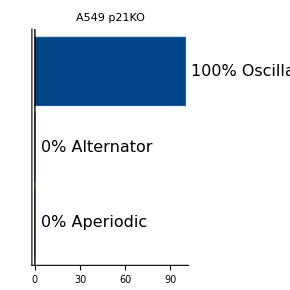

```mathematica
bar
```

### GTCF

Choose number of samples to plot

```mathematica
randchoice = 10;
```

```mathematica
randfit[rXout_]:= Module[{medpos,medp,medfit},
medpos= Round[SeedRandom[4214];RandomReal[Length[rXout],randchoice]];
medp= Table[Flatten[rXout[[medpos[[i]],1;;11]]],{i,1,randchoice}];
medfit = Transpose[Table[paras[[s]]->medp[[i]][[s]],{s,1,Length[paras]},{i,1,randchoice}]];
medfit
]
```

```mathematica
rt[rXout_]:= Module[{medpos,rt},
medpos= Round[SeedRandom[4214];RandomReal[Length[rXout],randchoice]];
rt = Table[If[rXout[[medpos[[i]],20]]==1,"fblue",If[rXout[[medpos[[i]],21]]==1,"fred", If[rXout[[medpos[[i]],22]]==1,"fyellow"]]],{i,1,randchoice}];
ToExpression[rt]
]
```

Split by behaviour

```mathematica
r1randout = randfit[r1out];//Quiet
r1randrt = rt[r1out];//Quiet
r2randout = randfit[r2out];//Quiet
r2randrt = rt[r2out];//Quiet
r3randout = randfit[r3out];//Quiet
r3randrt = rt[r3out];//Quiet
```

Define autocorrelation function

```mathematica
ω[k_,l_,paras_] := MatrixPower[theta/.paras,k].(omega0/.paras).MatrixPower[Transpose[theta/.paras],l]+MatrixPower[theta/.paras,k-1].(S2/.paras).MatrixPower[Transpose[theta/.paras],l-1];
```

```mathematica
A[k_,l_,paras_]:=Re[Total[Flatten[ω[k,l,paras]]]/Total[Flatten[omega0/.paras]]];
```

Functions for plotting tree correlation plots

```mathematica
randroutelcfcurve[paras_,col_,legend_,opac_]:=Module[{routelcfcurve},
routelcfcurve = ListLinePlot[Table[{n,A[n,0,paras]},{n,0,5,0.1}],PlotStyle->Directive[Opacity[opac],col,Thickness[.007],CapForm["Butt"]],PlotRange->{{0,5},{-1,1}},Frame->True,FrameLabel->{"Generation","Correlation"},PlotLabel->titlename,GridLines->Automatic,AlignmentPoint->{0,0},ImageSize->600,AspectRatio->1/3,LabelStyle->Directive[14]];
routelcfcurve
]
```

```mathematica
randroutebcfcurve[paras_,col_,legend_,opac_]:=Module[{routebcfcurve},
routebcfcurve = ListLinePlot[Table[{n+5,A[n,n,paras]},{n,0,3,0.05}],PlotStyle->Directive[Opacity[opac],col,Thickness[.007],CapForm["Butt"]],PlotRange->{{5,7},{-1,1}},Frame->True,GridLines->Automatic,AlignmentPoint->{0,0},ImageSize->400,AspectRatio->1/2,LabelStyle->Directive[14],FrameTicks->{{Automatic,Automatic},{{{1,"sister"},{2,"cousin"}},{1,1},{2,2}}}];
routebcfcurve
]
```

```mathematica
r1lcf = randroutelcfcurve[r1randout[[1]],r1randrt[[1]],1,1];//Quiet
r2lcf = randroutelcfcurve[r2randout[[1]],r2randrt[[1]],1,1];//Quiet
r3lcf = randroutelcfcurve[r3randout[[1]],r3randrt[[1]],1,1];//Quiet
r1bcf = randroutebcfcurve[r1randout[[1]],r1randrt[[1]],1,1];//Quiet
r2bcf = randroutebcfcurve[r2randout[[1]],r2randrt[[1]],1,1];//Quiet
r3bcf = randroutebcfcurve[r3randout[[1]],r3randrt[[1]],1,1];//Quiet
```

```mathematica
r1randplotlcf = Show[Table[randroutelcfcurve[r1randout[[i]],r1randrt[[i]],1,0.25],{i,1,randchoice}]];//Quiet
r1randplotbcf = Show[Table[randroutebcfcurve[r1randout[[i]],r1randrt[[i]],1,0.25],{i,1,randchoice}]];//Quiet
r2randplotlcf = Show[Table[randroutelcfcurve[r2randout[[i]],r2randrt[[i]],1,0.25],{i,1,randchoice}]];//Quiet
r2randplotbcf = Show[Table[randroutebcfcurve[r2randout[[i]],r2randrt[[i]],1,0.25],{i,1,randchoice}]];//Quiet
r3randplotlcf = Show[Table[randroutelcfcurve[r3randout[[i]],r3randrt[[i]],1,0.25],{i,1,randchoice}]];//Quiet
r3randplotbcf = Show[Table[randroutebcfcurve[r3randout[[i]],r3randrt[[i]],1,0.25],{i,1,randchoice}]];//Quiet
```

Tick labels

```mathematica
center=Row[{#,Invisible[#]},""]&;
fam = {Style["mother",LineSpacing->{.5,2},FontFamily->"Carlito"],Style["grandmother",LineSpacing->{.5,2},FontFamily->"Carlito"],Style["great\ngrandmother",LineSpacing->{.5,2},FontFamily->"Carlito"],Style["great great\ngrandmother",LineSpacing->{.5,2},FontFamily->"Carlito"],"",Style["sister",LineSpacing->{.5,2},FontFamily->"Carlito"],Style["cousin",LineSpacing->{.5,2},FontFamily->"Carlito"]};
xticks=Table[{n,center@Rotate[fam[[n]],40 Degree,{Right,Right}]},{n,1,7}];
```

```mathematica
txt1 = Text[Style["Lineage generation",16,FontFamily->"Carlito",Black,LineSpacing->{.7,2}],{2.5,1.5},{0,0}];
txt2 = Text[Style["Cross branch generation",16,FontFamily->"Carlito",Black,LineSpacing->{.7,2}],{6.2,1.5},{0,0}];
```

```mathematica
ttl = Text[Style[titlename,18,FontFamily->"Carlito",Black]];
```

```mathematica
bgframe =  ListPlot[{5,5},PlotRange->{{0,8},{-1,1}},Frame->True,FrameTicks->{{Automatic,Automatic},{xticks,{{0,0},{1,1},{2,2},{3,3},{4,4},{5,0},{6,1},{7,2}}}},FrameLabel->{{Style["Correlation",FontFamily->"Carlito"],None},{None,""}},GridLines->{{1,2,3,4,5,6,7},{-1,-0.5,0,0.5,1}},LabelStyle->Directive[16],AspectRatio->1/3,FrameStyle->Directive[Thick,Black],Epilog->{txt1,txt2},PlotRangeClipping->False,ImageSize->imagesize,ImagePadding->padding,PlotLabel->ttl];
```

```mathematica
divline = ListLinePlot[{{5,-1},{5,1}},PlotStyle->{Thickness[0.005],Black}];
```

```mathematica
corrdata = corrdata/."NaN"->Sequence[];
corrdata = corrdata/.{}->Sequence[];
```

```mathematica
corrdataplot = ListPlot[Table[{{1,2,3,4,6,7}[[s]],corrdata[[s]]},{s,1,6}],PlotMarkers->{"OpenMarkers"},PlotStyle->Black];
```

Plot GTCF

```mathematica
gtcfplot = Show[bgframe,r1randplotlcf,r2randplotlcf,r3randplotlcf,r1randplotbcf,r2randplotbcf,r3randplotbcf,r1lcf,r2lcf,r3lcf,r1bcf,r2bcf,r3bcf,divline,corrdataplot]
```

### Individual correlations

```mathematica
routecorrs[rXout_]:=Module[{med,lq,uq,routecorrs},
med = Median[rXout[[;;,12;;17]]];
lq = Quantile[rXout[[;;,12;;17]],0.025] -med;
uq = med - Quantile[rXout[[;;,12;;17]],0.975];
routecorrs = Table[Around[med[[i]],{lq[[i]],uq[[i]]}],{i,1,6}];
routecorrs
]
```

```mathematica
size = 2.5;
absoluteThickness = 0;
filledUpTriangle=Graphics[{Triangle[{Offset[size {0,2}+absoluteThickness {0,1}],Offset[size {Sqrt[3],-1}+absoluteThickness {Sqrt[3/4],-1/2}],Offset[size {-Sqrt[3],-1}+absoluteThickness {-Sqrt[3/4],-1/2}]}]},AlignmentPoint->{0,0}];
```

```mathematica
routecorrplot[rXout_,shift_,col_,legend_]:=Module[{routecorrplot,routecorrplotfit,routecorrplotpred},
routecorrplotfit = ListPlot[Table[{{1,2,6,7}[[s]]+shift,routecorrs[rXout][[{1,2,5,6}[[s]]]]},{s,1,4}],PlotStyle->col,PlotRange->{{0,9},{-1,1}},AlignmentPoint->{0,0},LabelStyle->Directive[14]];
routecorrplotpred = ListPlot[Table[{s+shift,routecorrs[rXout][[s]]},{s,{3,4}}],PlotRange->{{0,9},{-1,1}},AlignmentPoint->{0,0},PlotMarkers->{filledUpTriangle},LabelStyle->Directive[14],PlotStyle->col];
routecorrplot = Show[routecorrplotfit,routecorrplotpred]
]
```

```mathematica
routecorrplotlegend[rXout_,shift_,col_,legend_]:=Module[{routecorrplotlegend,routecorrplotfit,routecorrplotpred},
routecorrplotfit = ListPlot[Table[{{1,2,6,7}[[s]]+shift,routecorrs[rXout][[{1,2,5,6}[[s]]]]},{s,1,4}],PlotStyle->col,PlotRange->{{0,9},{-1,1}},AlignmentPoint->{0,0},PlotLegends->Placed[{Style[legend,FontFamily->"Carlito"]},Below],LabelStyle->Directive[14]];
routecorrplotpred = ListPlot[Table[{s+shift,routecorrs[rXout][[s]]},{s,{3,4}}],PlotRange->{{0,9},{-1,1}},AlignmentPoint->{0,0},PlotMarkers->{filledUpTriangle},LabelStyle->Directive[14],PlotStyle->col];
routecorrplotlegend = Show[routecorrplotfit,routecorrplotpred]
]
```

```mathematica
corrlegend = ListPlot[Table[{{1,2,3,4,6,7}[[s]],corrdata[[s]]},{s,1,6}],PlotMarkers->"OpenMarkers",PlotStyle->Black,LabelStyle->Directive[14],PlotLegends->Placed[{Style["Data",FontFamily->"Carlito"]},Below]];
dl = routecorrplotlegend[outputfile,0.15,Black,"Model fit"];//Quiet
r1l = routecorrplotlegend[r1out,0.15,fblue,"Route 1"];//Quiet
r2l = routecorrplotlegend[r2out,0.15,fred,"Route 2"];//Quiet
r3l = routecorrplotlegend[r3out,0.15,fyellow,"Route 3"];//Quiet
fig3leg = Show[corrlegend,dl,r1l,r2l,r3l];//Quiet
```

```mathematica
infplot = routecorrplot[outputfile,-0.15,Black,"Model Fit"];
r1plot = routecorrplot[r1out,0.15,fblue,"Route 1"];//Quiet
r2plot = routecorrplot[r2out,0.25,fred,"Route 2"];//Quiet
r3plot = routecorrplot[r3out,0.35,fyellow,"Route 3"];//Quiet
corrplot = Show[bgframe,corrdataplot,divline,infplot,r1plot,r2plot,r3plot];
```

```mathematica
corrplot
```

### Various underlying oscillator histograms

Find location of positive periods

```mathematica
posper = Select[Flatten[Position[Positive[Mean[r1out[[;;,;;]]]],True]],23≤#≤32&];
```

Text with calculated median and 95% CI overlaid

```mathematica
perds = Table[r1out[[;;,posper[[i]]]],{i,1,5}];
```

```mathematica
pervals = Median[Transpose[perds]];
```

```mathematica
loghist1 = SmoothHistogram[perds,Automatic,"PDF",Filling->Bottom,ImageSize->600,Frame->True, FrameLabel->{"Period (hours)","Probability"},LabelStyle->Directive[16],PlotStyle->Directive[EdgeForm[None]],GridLines->Automatic,PlotLabel->Style[titlename,Black,FontFamily->"Carlito"],FrameStyle->Directive[Black,Thick],AspectRatio->1/3,ScalingFunctions->{"Log","Log"},PlotRange->{{0,Max[pervals]+30},{0.01,Automatic}}];
```

```mathematica
pertable = Table[{{Log[pervals[[i]]],-100},{Log[pervals[[i]]],20}},{i,1,5}];
```

```mathematica
pertableplot = ListLinePlot[pertable,PlotStyle->Dashed];
```

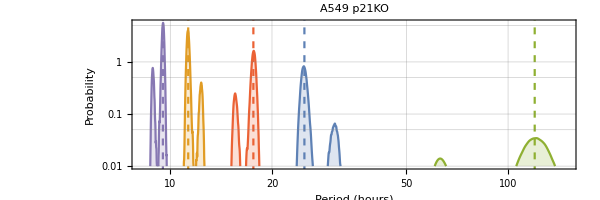

```mathematica
loghist = Show[loghist1,pertableplot]
```

```mathematica
underperiods = Reverse[pervals[[Ordering[pervals]]]]
```

{119.912,24.9459,17.6163,11.2978,9.50645}

## Plots

### Behaviour distribution

Bar chart indicating the distribution of behaviours for this dataset

```mathematica
bar
```

### Model fit

Correlations from data plotted alongside model fit and predictions for lineage generations 3 and 4

```mathematica
corrplot
```

### Generalised tree correlation function

Plot of 10 parameter samples producing the GTCF

```mathematica
gtcfplot
```

### Underlying periods

Possible underlying periods

```mathematica
loghist
```

Median of histograms, in large-small order

```mathematica
underperiods
```